# Visualizing Normalization

## A graphical presentation of NMR normalization methods.

Eric Moyer

Started 27 May 2012

## Introduction

Normalization methods in NMR spectrography (and probably other spectrographic fields as well) are typically explained by the procedures that you go through to perform them and justified by arguments about the "real concentration." Another way to look at normalization methods is to examine them as geometric operations on a vector space. This gives a different understanding of what is occurring, which can give the practitioner a deeper intuition about trade-offs he makes when he says, "sum-normalize the data."

I look at each spectrum generated as a point in a vector space, one variable in the vector for each value measured. I am mainly concerned with frequency-domain spectra, since it is on these that the normalization methods I present are typically used. The normalization methods do not solve extant problems on time-domain spectra, so they are not used there. However, my points are just as valid for time-domain spectra, since they too are vectors.

## Sum Normalization

Sum normalization takes each spectrum, divides it by its sum, and then multiplies it by a constant. After this operation, all spectra have the same sum.

If the spectra are interpreted as points in an n-dimensional vector space, this projects all points onto an n-1 dimensional subspace (hyperplane) along a line between the original point and the origin. In 3 dimensions, it projects points onto a the plane x+y+z=s . In 2 dimensions, all points are projected the line y=s-x. The location of these figures is determined by the constant.

How can we see this?

First, consider that multiplying a (non-zero) point by a constant moves it along a line connecting the point with the origin. Multiplying by a positive number less than 1 moves it closer to the origin. Multiplying by a number greater than 1 moves farther from the origin. And multiplying it by a negative number moves it away from the origin on the opposite side.

```mathematica
xPlusYEq1TwoD=Plot[{1-x},{x,-1,2},PlotStyle->Red];
```

```mathematica
yEq2X=Plot[{2x},{x,0,3/2},PlotStyle->Darker[Blue]];
```

```mathematica
ptX3HalvesY3AndProjection=ListPlot[{{{3/2,3}},{{1/3,2/3}}},PlotMarkers->{Automatic,Medium},PlotStyle->{Darker[Blue],Darker[Magenta]}];
```

```mathematica
firstDiagram=Show[{xPlusYEq1TwoD,Graphics[{Text["Constant sum surface",{0.6,0.5},{-1,0},BaseStyle->{Red}],Text["Spectrum",{3/2,11/4},{-1,0},BaseStyle->{Darker[Blue]}]}],yEq2X,ptX3HalvesY3AndProjection},PlotRange->All,AspectRatio->Automatic,ImageSize->{300},PlotRangeClipping->False];
```

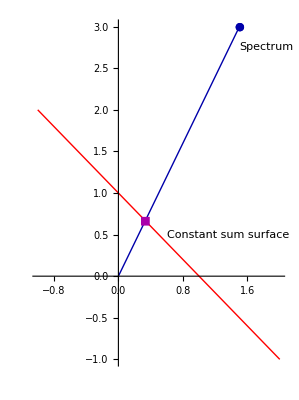
-Graphics-Figure 1: Sum Normalization in Two Dimensions

```mathematica
firstDiagramWithCaption=Labeled[firstDiagram,"Figure 1: Sum Normalization in Two Dimensions",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

The point at which the line through the origin intersects with the surface of points whose sum equals the target sum of the sum-normalization is the normalized point. Figures 1 and 2 show sum-normalization in two and three dimensions with a target sum of 1.

```mathematica
sumEq1ThreeD=Graphics3D[{Opacity[0.85],Red,Polygon[{{-1,-1,3},{1,-1,1},{1,1,-1},{-1,1,1}}]},Axes->True];
```

```mathematica
yEq2XThreeD=Graphics3D[{Darker[Blue],Line[{{0,0,0},{3/2,0,3}}],PointSize[Large],Point[{3/2,0,3}],Text["Origin",{0,0,0},{-1.2,0}],Darker[Magenta],Point[{1/3,0,2/3}]}];
```

```mathematica
secondDiagram=Show[{sumEq1ThreeD,yEq2XThreeD}];
```

```mathematica
secondDiagramWithCaption=Labeled[secondDiagram,"Figure 2: Sum Normalization in Three Dimensions",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

-Graphics3D-Figure 2: Sum Normalization in Three Dimensions

## Probabilistic Quotient Normalization

Probabilistic Quotient Normalization (PQN) (Dieterle 2006) is a method that is more resistant to large fluctuations in parts of the spectrum due to factors other than dilution (such as treatments). Unlike sum-normalization, which normalizes each spectrum independently, PQN is designed to normalize several related spectra simultaneously, using their commonality to improve its estimates.

PQN starts with sum-normalization. Next, the spectra are binned to take care of small peak-shifts. Then a reference spectrum is created. The original paper mentions several methods of creating reference spectra. However, for simplicity, we will choose the method that takes the median spectrum of all the spectra being analyzed. Then, for each spectrum to be normalized, the reference spectrum is divided by it and the median of the quotients is selected as the normalization factor. Finally the spectra are multiplied by their respective normalization factors.

For the following discussion, we will assume that the initial spectra have no negative values. Negative values result from noise or special acquisition methods like dephasing the water signal and should be removed during preprocessing. Though PQN is well-defined with negative values, their inclusion unnecessarily complicates the explanation.

### 2D PQN (the canonical way)

#### Sum Normalize

The first step of PQN we've seen before, we sum-normalize. In the diagrams, I sum-normalize to 1, since it is easy, but everything works out the same, just scaled a bit differently if you sum-normalize to a different constant.

```mathematica
orig2D={{2.172454345958343,1.7744919345405104},{2.675301724350803,1.359406145521423},{2.87830990460933,1.4709889319173473},{2.8813454193984884,1.073276896492814},{2.3606473361385762,1.7882842580601983},{2.26005835257858,1.7655977040112563},{1.398151988227432,2.097238014713233},{3.0861624358478528,0.9274842729247682},{2.255768229218814,1.8706253682049265},{2.6917625635090703,1.2898265639379862}};
```

```mathematica
sumNorm2D=Map[#/Total[#]&,orig2D];
```

```mathematica
thirdDiagram=Graphics[{PointSize->Medium,Darker[Blue],Map[Point[#]&,orig2D],Map[Line[{{0,0},#}]&,orig2D],Darker[Magenta],Map[Point[#]&,sumNorm2D],Red,Line[{{1,0},{0,1}}]},Axes->True];
```

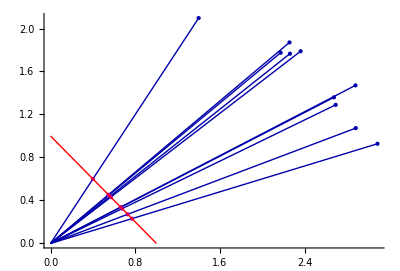
-Graphics-Figure 3: First step of 2D PQN: Sum-Normalize

```mathematica
thirdDiagramWithCaption=Labeled[thirdDiagram,"Figure 3: First step of 2D PQN: Sum-Normalize",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

#### Reference Spectrum

Next, you generate a reference spectrum by taking the median of each variable.

```mathematica
refPt2D=Map[Median,Transpose[sumNorm2D]]
```

{0.615382,0.384618}

```mathematica
fourthDiagram=Graphics[{PointSize[Medium],Darker[Magenta],Map[Point[#]&,sumNorm2D],Red,Line[{{1,0},{0,1}}],Green,PointSize[Large],Point[refPt2D],Text["Reference spectrum",{0.025,0}+refPt2D,{-1,0}]},Axes->True];
```

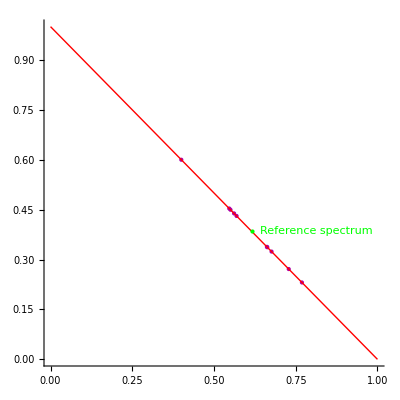
-Graphics-Figure 4: Second step of 2D PQN: Create reference spectrum

```mathematica
fourthDiagramWithCaption=Labeled[fourthDiagram,"Figure 4: Second step of 2D PQN: Create reference spectrum",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

#### Reciprocal Quotient Spectra

In the next step, I make a change to the procedure that makes it easier to understand. Rather than dividing the reference spectrum by each of the individual spectra to get the quotient spectra, I divide each spectrum by the reference spectrum. This leaves me with quotient spectra that have the reciprocals of the proper coordinates. Because all of the individual coordinates are positive, this just reverses their ranks. The median element will still be the same. So, I can just divide by the median rather than multiplying to get the same final normalization. In the case of an even number of points, you can't get the reciprocal of the average by taking the average of the reciprocals. Thus, if the center two reciprocal quotients are a and b the reciprocal quotient median is m=(2a b)/(a+b)

```mathematica
standardQuotientTransformPlot=ParametricPlot[{{t,1-t},{refPt2D[[1]]/t,refPt2D[[2]]/(1-t)}},{t,0.001,1},AspectRatio->Automatic,PlotRange->{{0,3},{0,3}},ColorFunction->Function[{x,y,u},Hue[u/1.1]],PlotStyle->Thickness[0.025]];
```

```mathematica
standardQuotientArrows=Graphics[{Thickness[Small],Flatten[Map[{Hue[#],Arrow[{{#,1-#},{refPt2D[[1]]/#,refPt2D[[2]]/(1-#)}},{0,.9Abs[refPt2D[[1]]-#]}]}&,refPt2D[[1]]+{-0.15,-0.06,0.06,0.15}]]}];
```

```mathematica
fifthDiagram=Show[{standardQuotientTransformPlot,standardQuotientArrows,Graphics[{Text["Sum-normalized spectra",{1,0.2},{-1,0}],Text["Quotient spectra using standard method",{.9,2.5},{-1,0}],Text["Colors give correspondence (note reversal)",{0.9,2.36},{-1,0}] }]}];
```

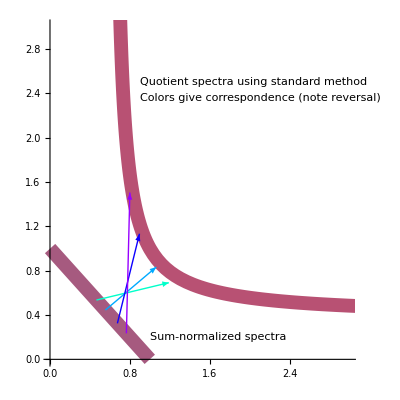
-Graphics-Figure 5: Standard method of creating quotient spectra

```mathematica
fifthDiagramWithCaption=Labeled[fifthDiagram,"Figure 5: Standard method of creating quotient spectra",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

```mathematica
linearQuotientTransformPlot=ParametricPlot[{{t,1-t},{t/refPt2D[[1]],(1-t)/refPt2D[[2]]}},{t,0.001,1},AspectRatio->Automatic,PlotRange->{{0,3},{0,3}},ColorFunction->Function[{x,y,u},Hue[u/1.1]],PlotStyle->Thickness[0.025]];
```

```mathematica
linearQuotientArrows=Graphics[{Thickness[Small],Flatten[Map[{Hue[#],Arrow[{{#,1-#},{#/refPt2D[[1]],(1-#)/refPt2D[[2]]}},0.1]}&,refPt2D[[1]]+{-.25,-0.15,-0.06,0.06,0.15,0.25}]]}];
```

```mathematica
sixthDiagram=Show[{linearQuotientTransformPlot,linearQuotientArrows,Graphics[{Text["Sum-normalized",{1.1,0.1},{-1,0}],Text["Reciprocal Quotient spectra",{0.4,2.29},{-1,0}],Text["Colors give correspondence",{0.4,2.15},{-1,0}] }]}];
```

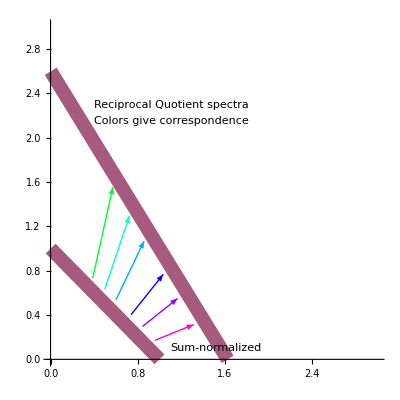
-Graphics-Figure 6: Easy-to-visualize method of creating reciprocal quotient spectra

```mathematica
sixthDiagramWithCaption=Labeled[sixthDiagram,"Figure 6: Easy-to-visualize method of creating reciprocal quotient spectra",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

The standard method involves three non-linear transformations of the spectral space, one to create the quotient spectra and then another to extract their medians, and a third to multiply the corresponding spectra by their medians. My method involves only two non-linear transformations - extracting the medians and dividing by them. The creation of the reciprocal quotient  (r-quotient) spectra is a linear transformation. Further, my method of creating the quotients does not flip the axes. This makes my method much easier to visualize. You can compare the two methods of creating the quotient spectra by looking at figures 5 and 6 (these diagrams are created using the reference spectrum from figure 4).

#### Median Reciprocal Quotients

```mathematica
Simplify[Solve[{z==2c d/(c+d),c==x,d==m x+b},{z},{c,d}]]
```

{{z→(2 x (b+m x))/(b+x+m x)}}

```mathematica
FullSimplify[Solve[{z==2c d/(c+d),c==x,d==(r x)/(r-1)+1/(1-r)},{z},{c,d}]]
```

{{z→-(2 x (-1+r x))/(1+x-2 r x)}}

```mathematica
(r x)/(r-1)+1/(1-r)
```

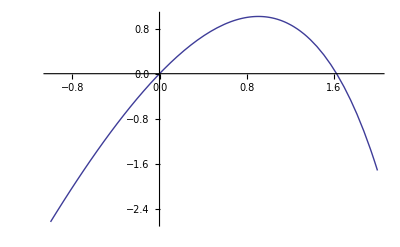

```mathematica
With[{r=refPt2D[[1]]},Plot[{-(2 x (-1+r x))/(1+x-2 r x)},{x,-1,2}]]
```

```mathematica
Manipulate[Plot[{(2 x (1-r x))/(1+x-2 r x)},{x,0,1},PlotRange->{-1,2}],{r,0,1}]
```

```mathematica
(2 x (1-r x))/(1+x-2 r x)/.r->1
```

2 x

```mathematica
(1-r x)/(1+x-2 r x)
```

(1-r x)/(1+x-2 r x)

```mathematica
Reduce[1+x-2 r x==0]
```

x≠0&&r==(1+x)/(2 x)

```mathematica
Solve[r==(1+x)/(2 x),{x}]
```

{{x→1/(-1+2 r)}}

```mathematica
Simplify[(1+x-2 r x)/(x-1/(-1+2 r))]
```

1-2 r

```mathematica
Simplify[(1-2r)(x-1/(-1+2 r))]
```

1+x-2 r x

After generating the r-quotient spectra, the next step is to take the median of the r-quotients, that is, the median of all of the coordinates of each spectrum. The r-quotient spectra lie on the line between (1/r,0) and (0,1/(1-r)). This line is y=r/(r-1)x+1/(1-r). Applying the reciprocal median formula above to the points on the r-quotient  line (q, r/(r-1)q+1/(1-r)) we get m=2 q (1-r q)/(1+q-2 r q).

```mathematica
rMedianAndRQuotientCurve=With[{r=refPt2D[[1]]},ParametricPlot[{{q,(r q)/(r-1)+1/(1-r)},{q,(r q)/(r-1)+1/(1-r)}+((2q(1-r q))/(1+q-2r q))quotientLineUnitNormal},{q,0,1/r}]];
```

```mathematica
Module[{rqpt,r},
r=refPt2D[[1]];
rqpt[q_]:={{q,(r q)/(r-1)+1/(1-r)},{q,(r q)/(r-1)+1/(1-r)}+((2q(1-r q))/(1+q-2r q))quotientLineUnitNormal};
rMedianRQuotientArrows=Graphics[{Blue,Map[Arrow[rqpt[#]]&,1/refPt2D[[1]]{0.125,0.25,0.375,0.5,0.625,0.75,0.875}]}]
];
```

```mathematica
quotientLineLeftEndpoint={0,1/refPt2D[[2]]};
```

```mathematica
quotientLineRightEndpoint={1/refPt2D[[1]],0};
```

```mathematica
quotientLineUnitNormal=Reverse[Normalize[quotientLineRightEndpoint-quotientLineLeftEndpoint]]{-1,1};
```

```mathematica
seventhDiagram=Show[rMedianAndRQuotientCurve,rMedianRQuotientArrows];
```

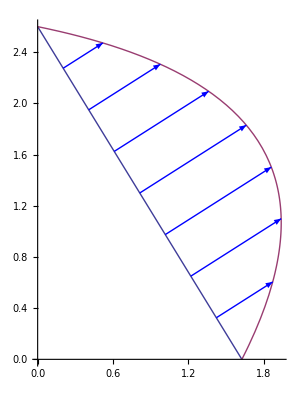
-Graphics-Figure 7: Median r-quotient as distance perpendicular to r-quotient line.

```mathematica
seventhDiagramWithCaption=Labeled[seventhDiagram,"Figure 7: Median r-quotient as distance perpendicular to r-quotient line. ",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

#### Move Median R-Quotients

The median r-quotients in the previous step are displayed attached to their corresponding reciprocal quotient points. But they should be attached to the sum-normalized points. The next step matches the median quotients back to the original points. Substituting q=x/r into the median equation above yields m=(2 (1-x) x)/(r+x-2 r x)=(2x (1-x))/(r(1-x)+x(1-r))=(2x y)/(x(1-r)+y r)

```mathematica
FullSimplify[Solve[{m==(2q(1-r q))/(1+q-2r q),q==x/r},{m},{q}]]
```

```mathematica
{{m->(2 (1-x) x)/(r+x-2 r x)}}
```

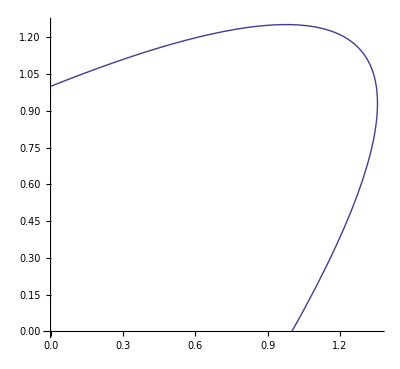

```mathematica
sumNormAppropriateMedianCurve=With[{r=refPt2D[[1]]},ParametricPlot[{x,1-x}+(2 (1-x) x)/(r+x-2 r x)Normalize[{1,1}],{x,0,1}]]
```

```mathematica
sumNormPointsPlot=Graphics[{PointSize[Medium],Darker[Magenta],Map[Point[#]&,sumNorm2D],Red,Line[{{1,0},{0,1}}]},Axes->True];
```

```mathematica
ninthDiagram=Show[sumNormAppropriateMedianCurve,sumNormPointsPlot,Options[sumNormPointsPlot]];
```

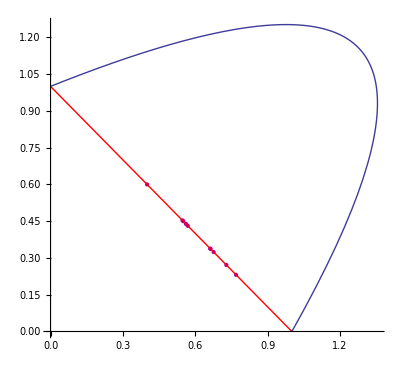
-Graphics-Figure 9: Sum-normalized points with their r-quotient scaling factors above them.

```mathematica
ninthDiagramWithCaption=Labeled[ninthDiagram,"Figure 9: Sum-normalized points with their r-quotient scaling factors above them.",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

#### Scale Sum-Normalized Points

The final step is to divide each spectrum by its corresponding reciprocal quotient. This results in the curve y=((-1+r) x)/(r-2 x) on the interval [r/2,∞). (Note that there is a y asymptote as well aty=(1-r)/2. The scaled spectra are the intersections of this curve with the lines connecting the original points and the origin.

```mathematica
Simplify[Solve[{x==t/((2 (1-t) t)/(r+t-2 r t)),y==(1-t)/((2 (1-t) t)/(r+t-2 r t))},{y},{t}]]
```

{{y→((-1+r) x)/(r-2 x)}}

```mathematica
Simplify[t/((2 (1-t) t)/(r+t-2 r t))]
```

(r+t-2 r t)/(2-2 t)

```mathematica
Solve[x==(r+t-2 r t)/(2-2 t),{t}]
```

{{t→(r-2 x)/(-1+2 r-2 x)}}

```mathematica
y==(1-t)/((2 (1-t) t)/(r+t-2 r t))/.{{t->(r-2 x)/(-1+2 r-2 x)}}
```

{y==((r+(r-2 x)/(-1+2 r-2 x)-(2 r (r-2 x))/(-1+2 r-2 x)) (-1+2 r-2 x))/(2 (r-2 x))}

```mathematica
FullSimplify[y==((r+(r-2 x)/(-1+2 r-2 x)-(2 r (r-2 x))/(-1+2 r-2 x)) (-1+2 r-2 x))/(2 (r-2 x))]
```

((-1+r) x)/(r-2 x)==y

```mathematica
refPt2D/2
```

{0.307691,0.192309}

```mathematica
Simplify[{t,1-t}/((2 (1-t) t)/(r+t-2 r t))]
```

{(r+t-2 r t)/(2-2 t),(r+t-2 r t)/(2 t)}

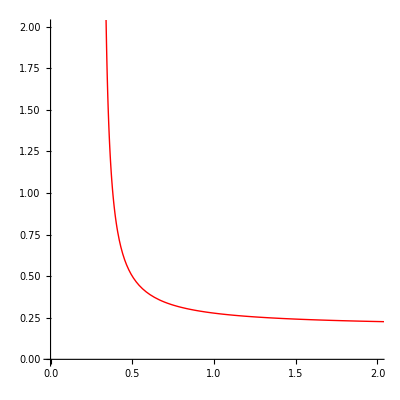

```mathematica
bar=With[{r=refPt2D[[1]]},ParametricPlot[{(r+t-2 r t)/(2-2 t),(r+t-2 r t)/(2 t)},{t,0.01,0.99},PlotRange->{{0,2},{0,2}},AspectRatio->Automatic,PlotStyle->Red]]
```

```mathematica
Limit[(r+t-2 r t)/(2-2 t),t->0](*X asymptote*)
```

r/2

```mathematica
Limit[(r+t-2 r t)/(2 t),t->1](*Y asymptote*)
```

(1-r)/2

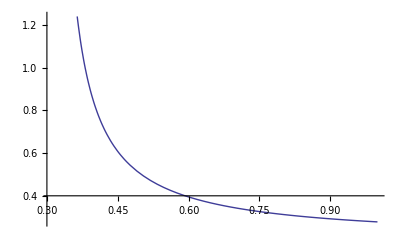

```mathematica
foo=With[{r=refPt2D[[1]]},Plot[((-1+r) x)/(r-2 x),{x,r/2,1}]]
```

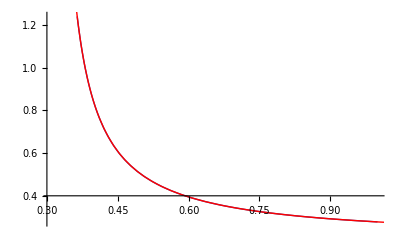

```mathematica
Show[{foo,bar}]
```

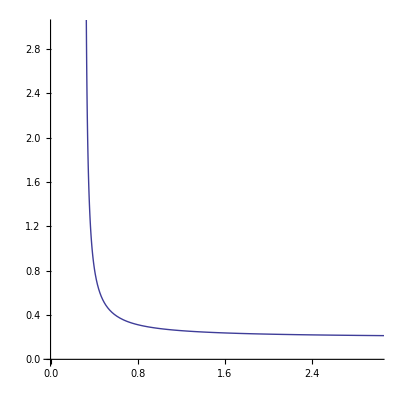

```mathematica
medianScaledSumNorm=With[{r=refPt2D[[1]]},ParametricPlot[{t,1-t}/((2 (1-t) t)/(r+t-2 r t)),{t,0.01,0.99},PlotRange->{{0,3},{0,3}}]]
```

```mathematica
rQuotientForX2D[x_,refPt_]:=With[{xQuot=x/refPt[[1]],yQuot=(1-x)/refPt[[2]]},
(xQuot+yQuot)/2]
```

##### A digression on the form of the reciprocal median quotient curve

There were two interesting characteristics of the median quotients. First, the median quotient is 1for exactly two spectra for any given reference spectrum. First, the reference spectrum is given a quotient of 1. Second (unless the reference spectrum has a 0) is the spectrum with all equal heights (normalized x=1/2) is also always unchanged for two dimensional spectra.

```mathematica
Simplify[Reduce[(2 (1-x) x)/(r+x-2 r x)==1&&0≤x≤1&&0≤r≤1,{x}]]
```

(r==x&&(0<r<1/2||1/2<r<1))||(2 x==1&&0≤r&&r≤1)

Second, the maximum reciprocal quotient is located along a lovely s-shaped curve.

```mathematica
Reduce[D[(2 (1-x) x)/(r+x-2 r x),x]==0&&0≤x≤1&&0≤r≤1,{x}]
```

(0<r<1/2&&x==r/(-1+2 r)+√((r-r^2)/(-1+2 r)^2))||(r==1/2&&x==1/2)||(1/2<r<1&&x==r/(-1+2 r)-√((r-r^2)/(-1+2 r)^2))

```mathematica
Reduce[D[(2 (1-x) x)/(r+x-2 r x),x]==0&&0≤x≤1&&0≤r≤1]
```

0<x<1&&r==x^2/(1-2 x+2 x^2)

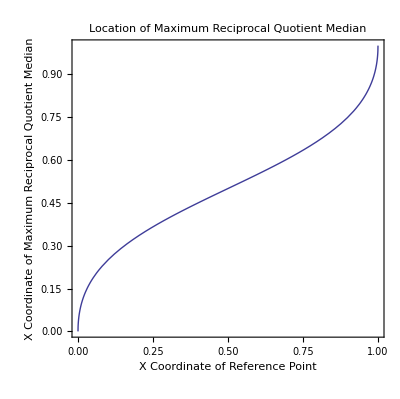

```mathematica
Plot[Which[0<r<1/2,r/(-1+2 r)+√((r-r^2)/(-1+2 r)^2),
r==1/2,1/2,1/2<r<1,r/(-1+2 r)-√((r-r^2)/(-1+2 r)^2)],{r,0,1},Frame->{True,True,False,False},AspectRatio->Automatic,FrameLabel->{"X Coordinate of Reference Point", "X Coordinate of Maximum Reciprocal Quotient Median"},PlotLabel->"Location of Maximum Reciprocal Quotient Median"]
```

### 2D PQN (the easy way)

Because 2D is such a special case (the median is the same as the mean and the reference spectrum can be specified by one variable), the entire normalization procedure can be viewed in two simple steps. First, sum normalize as before and choose the reference spectrum.

```mathematica
eleventhDiagramWithCaption=Labeled[fourthDiagram,"Figure 11: Points sum-normalized with reference spectrum",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

-Graphics-Figure 11: Points sum-normalized with reference spectrum

For any point sum-normalized to the coordinates, (x_sn,1-x_sn) and when the reference spectrum is (r,1-r), the r-quotient is 1/2((1-x_sn)/(1-r)+x_sn/r)which makes the normalization factor ((2 r-2) r)/(x_sn(2 r-1)-r).

This means that the final coordinates are x=-(2 (-1+r) r x_sn)/(r+x_sn-2 r x_sn) and y=-(2 (-1+r) r (-1+x_sn))/(-x_sn+r (-1+2 x_sn)). When we eliminate x_sn, we arrive at a line: y=(r-1)/r x+2(1-r). Noting that 1-r is the y coordinate of the reference point, we can rewrite this as:

y=2 r_y-r_y/r_x x

This is the line between the two points (0, 2 r_y) and (2 r_x,0). The final scaled points are just the intersections between this line and the lines to the original points. Thus, in two dimensions, when all spectra have only positive coordinates, we can look at PQN as just replacing the sum normalization line y=1-x with the line y=2 r_y-r_y/r_x x derived from the reference spectrum. This is easiest to visualize if we imagine sum-normalizing to 2 rather than 1 and then producing the line directly from the coordinates of the reference point.

```mathematica
pqn2D[point_,refPt_]:=With[{t=point[[1]]/Total[point],r=refPt[[1]]},{-(2 (-1+r) r t)/(r+t-2 r t),-(2 (-1+r) r (-1+t))/(-t+r (-1+2 t))}]
```

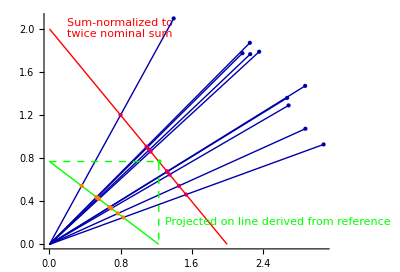

```mathematica
twelfthDiagram=Graphics[{PointSize->Medium,Darker[Blue],Map[Point[#]&,orig2D],Map[Line[{{0,0},#}]&,orig2D],Darker[Magenta],Map[Point[#]&,2sumNorm2D],Red,Line[{{2,0},{0,2}}],Text["Sum-normalized to",{0.2,2.1},{-1,1}],Text["twice nominal sum",{0.2,2.0},{-1,1}],PointSize[Medium],Green,Point[2 refPt2D],Line[{{0,2refPt2D[[2]]},{2refPt2D[[1]],0}}],Dashed,Line[{{0,2refPt2D[[2]]},2refPt2D,{2refPt2D[[1]],0}}],
Text["Projected on line derived from reference",{1.3,0.25},{-1,1}],Orange,Map[Point[pqn2D[#,refPt2D]]&,orig2D]},Axes->True]
```

```mathematica
Solve[0==2 ry-ry/rx x,{x}]
```

{{x→2 rx}}

```mathematica
rQuotientForX2D[t,{r,1-r}]/.t->Subscript[x, sn]
```

1/2 ((1-x_sn)/(1-r)+x_sn/r)

```mathematica
FullSimplify[1/rQuotientForX2D[t,{r,1-r}]]/.t->Subscript[x, sn]
```

-(2 (-1+r) r)/(r+x_sn-2 r x_sn)

```mathematica
Simplify[(1-t)/rQuotientForX2D[t,{r,1-r}]]
```

-(2 (-1+r) r (-1+t))/(-t+r (-1+2 t))

```mathematica
Simplify[t/rQuotientForX2D[t,{r,1-r}]]/.t->Subscript[x, sn]
```

-(2 (-1+r) r x_sn)/(r+x_sn-2 r x_sn)

```mathematica
Simplify[(1-t)/rQuotientForX2D[t,{r,1-r}]]/.t->Subscript[x, sn]
```

-(2 (-1+r) r (-1+x_sn))/(-x_sn+r (-1+2 x_sn))

```mathematica
FullSimplify[Solve[x==FullSimplify[(x/.Solve[{x==-(2 (-1+a) a t)/(a+t-2 a t),y==-(2 (-1+a) a (-1+t))/(-t+a (-1+2 t))},{x,y},{t}])[[1]]]/.a->r,{y}]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→2-2 r+x-x/r}}